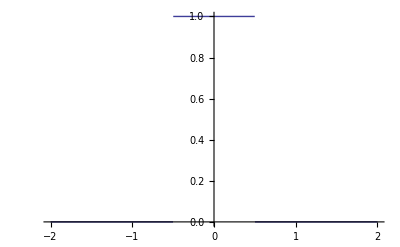

```mathematica
rect[t_]:=UnitStep[t+1/2]-UnitStep[t-1/2];
Plot[rect[t],{t,-2,2}]
```

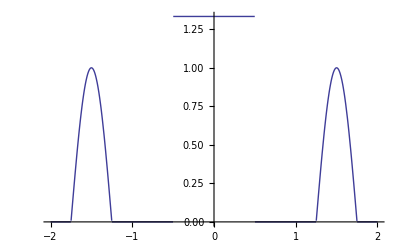

```mathematica
Fx[f_]:=4*rect[f]/3-Cos[2*Pi*f]*(rect[2*f-3]+rect[2*f+3]);
Plot[Fx[f],{f,-2,2}]
```

(2 √(2 π) Cos[(5 t)/4])/(4 π^2-t^2)+(2 √(2 π) Cos[(7 t)/4])/(4 π^2-t^2)+(4 √(2/π) Sin[t/2])/(3 t)

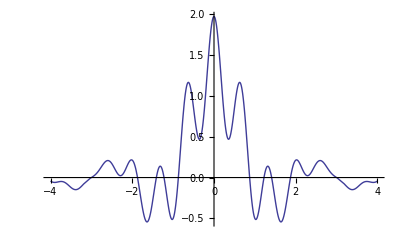

```mathematica
xomega[t_]=InverseFourierTransform[Fx[f],f,t]
x[t_]:=Sqrt[2*Pi]*xomega[2*Pi*t];
Plot[x[t],{t,-4,4}]
```

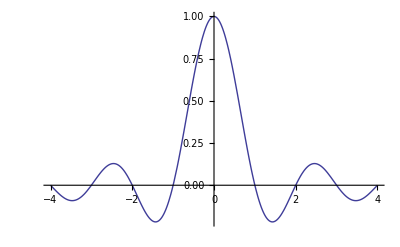

```mathematica
sincpi[t_]:=Sinc[Pi*t];
Plot[sincpi[t],{t,-4,4}]
```

```mathematica
myx[t_]:=4*sincpi[t]/3+(1/2)*Cos[3*Pi*t]*(sincpi[(t+1)/2]+sincpi[(t-1)/2]);
Plot[myx[t],{t,-4,4},PlotRange->All]
```

-Graphics-

-(ⅈ ⅇ^(-(ⅈ t)/4) (-1+ⅇ^((ⅈ t)/2)))/(√(2 π) t)

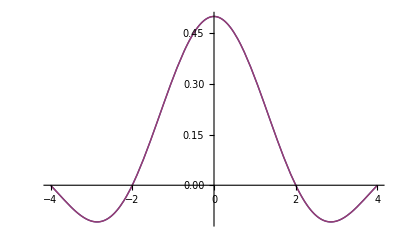

```mathematica
Fa[t_]:=rect[2*f];
aomega[t_]=InverseFourierTransform[Fa[f],f,t]
a[t_]:=Sqrt[2*Pi]*aomega[2*Pi*t];
mya[t_]:=sincpi[t/2]/2;
Plot[{a[t],mya[t]},{t,-4,4}]
```

```mathematica
testb[t_]:=Cos[3*Pi*t]*a[t];
```